```mathematica
n=20;h=0.1;
a=1;b=1+2/10;c=35/100;w=1.5;
m=SparseArray[{Band[{1,2}]->-a,Band[{2,1}]->-b,Band[{1,1}]->a+b+c},{n,n}];
mm=IdentityMatrix[n]-h m;
p[t_]:=((1+0.8Cos[2π t/n])/Sqrt[π])^3;
mm=SparseArray[{{i_,i_}->p[i+0.5]^3+p[i-0.5]^3},{n,n}]

 Bpsor=PSORSplitting[mm,w];

q=RandomReal[{-1,1},n];
```

SparseArray[<20>,{20,20}]

```mathematica
q=Table[(i-n/2)^2-n,{i,n}]//N
```

{61.,44.,29.,16.,5.,-4.,-11.,-16.,-19.,-20.,-19.,-16.,-11.,-4.,5.,16.,29.,44.,61.,80.}

```mathematica
mm//MatrixForm//N
```

(0.775 | 0.1 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.12 | 0.775 | 0.1 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.12 | 0.775 | 0.1 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0.12 | 0.775 | 0.1 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.12 | 0.775 | 0.1 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.12 | 0.775 | 0.1 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.12 | 0.775 | 0.1 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.12 | 0.775 | 0.1 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.12 | 0.775 | 0.1 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.12 | 0.775 | 0.1 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.12 | 0.775 | 0.1 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.12 | 0.775 | 0.1 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.12 | 0.775 | 0.1 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.12 | 0.775 | 0.1 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.12 | 0.775 | 0.1 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.12 | 0.775 | 0.1 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.12 | 0.775 | 0.1 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.12 | 0.775 | 0.1 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.12 | 0.775 | 0.1 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.12 | 0.775 | 0.1 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.12 | 0.775 | 0.1 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.12 | 0.775 | 0.1 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.12 | 0.775 | 0.1 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.12 | 0.775 | 0.1 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.12 | 0.775 | 0.1 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.12 | 0.775 | 0.1 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.12 | 0.775 | 0.1 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.12 | 0.775 | 0.1 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.12 | 0.775 | 0.1 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.12 | 0.775 | 0.1 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.12 | 0.775 | 0.1 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.12 | 0.775 | 0.1 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.12 | 0.775 | 0.1 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.12 | 0.775 | 0.1 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.12 | 0.775 | 0.1 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.12 | 0.775 | 0.1 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.12 | 0.775 | 0.1 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.12 | 0.775 | 0.1 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.12 | 0.775 | 0.1 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.12 | 0.775 | 0.1 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.12 | 0.775 | 0.1 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.12 | 0.775 | 0.1 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.12 | 0.775 | 0.1 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.12 | 0.775 | 0.1 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.12 | 0.775 | 0.1 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.12 | 0.775 | 0.1 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.12 | 0.775 | 0.1 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.12 | 0.775 | 0.1 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.12 | 0.775 | 0.1
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.12 | 0.775)

```mathematica
{dkasd,sol}=LCPviaQP[q,mm]
```

{2.37454×10^-7,{7.30685×10^-12,8.02381×10^-12,8.85577×10^-12,9.82968×10^-12,1.09812×10^-11,1.23582×10^-11,1.4027×10^-11,1.60812×10^-11,1.86573×10^-11,2.19623×10^-11,2.63247×10^-11,3.22975×10^-11,4.08873×10^-11,5.41325×10^-11,7.68682×10^-11,1.23981×10^-10,2.74418×10^-10,8.24774×10^-8,14.7727,25.5113,34.5598,41.5477,46.5335,49.508,50.4727,49.4272,46.3718,41.3059,34.2328,25.1286,14.1736,1.94251×10^-8,2.74544×10^-10,1.23981×10^-10,7.68682×10^-11,5.41325×10^-11,4.08873×10^-11,3.22975×10^-11,2.63247×10^-11,2.19623×10^-11,1.86573×10^-11,1.60812×10^-11,1.4027×10^-11,1.23582×10^-11,1.09812×10^-11,9.82968×10^-12,8.85577×10^-12,8.02381×10^-12,7.30685×10^-12,6.68418×10^-12}}

```mathematica
{l2,n2,m2,o2,p2}=Table[1,{i,5},{j,n}];
```

```mathematica
w2=h/2;{m1,m2,m3}=IterativeSplitting[60,IdentityMatrix[n]+w2 m,mm,q,m2];
```

```mathematica
{l1,l2,l3}=IterativeSplitting[60,Bpsor,mm,q,l2];
```

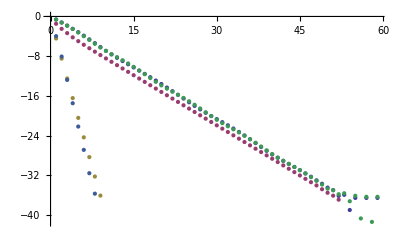

```mathematica
ListPlot[Log[{l3,m3,n3,o3,p3}]]
```

```mathematica
{n1,n2,n3}=IterativeSplitting[60,0.5(mm+Transpose[mm]),mm,q,n2];
```

```mathematica
{p1,p2,p3}=IterativeSplitting[60,Partition[Max/@Transpose[{Flatten[mm],Flatten[Transpose[mm]]}],n],mm,q,p2];
```

```mathematica
{o1,o2,o3}=IterativeSplitting[60,PSORSplitting[0.5(mm+Transpose[mm]),w],0.5(mm+Transpose[mm]),q,o2]
```

{5.97351×10^-7,{2.91741×10^-8,0.413579,6.60768×10^-9,7.93436×10^-8,2.99806×10^-8,7.69113×10^-9,7.82041×10^-9,0.865673,6.19632×10^-9,0.740058,1.10117,1.53992×10^-8,2.78505×10^-8,0.050084,0.0110573,1.62927×10^-8,2.04862×10^-7,0.00945209,9.16891×10^-9,8.25946×10^-9},{0.537155,0.291289,0.155033,0.0798458,0.0396006,0.0189367,0.00880275,0.00405705,0.0019175,0.000959679,0.000508292,0.000275763,0.000148212,0.0000774052,0.0000389723,0.0000188966,8.86867×10^-6,4.08771×10^-6,1.90413×10^-6,9.29567×10^-7,4.82791×10^-7,2.60647×10^-7,1.41047×10^-7,7.46093×10^-8,3.81279×10^-8,1.87595×10^-8,8.90846×10^-9,4.12479×10^-9,1.90511×10^-9,9.09546×10^-10,4.6138×10^-10,2.464×10^-10,1.3373×10^-10,7.15219×10^-11,3.70798×10^-11,1.85192×10^-11,8.91212×10^-12,4.15987×10^-12,1.91609×10^-12,8.98878×10^-13,4.44703×10^-13,2.33603×10^-13,1.26482×10^-13,6.82547×10^-14,3.58245×10^-14,1.81972×10^-14,8.78033×10^-15,4.15555×10^-15,1.96022×10^-15,8.60157×10^-16,6.25038×10^-16,2.79692×10^-16,3.39192×10^-16,6.7882×10^-17,2.03734×10^-16,2.12048×10^-18,1.66313×10^-16,1.05928×10^-18,1.66148×10^-16,0.}}

```mathematica
PSOR[50,1-h*(c+a+b),h b,h a,q,1.5,mm]
```

0.

1.89326

-0.442622

0.290588

-0.103635

0.0490648

-0.0188201

0.00797326

-0.00310478

0.00129713

-0.00054775

0.000256142

-0.000128649

0.0000697261

-0.0000388906

0.0000217891

-0.0000119587

6.35395×10^-6

-3.2348×10^-6

1.56464×10^-6

-7.10119×10^-7

2.95945×10^-7

-1.07938×10^-7

2.97517×10^-8

-1.39163×10^-9

-6.30008×10^-9

6.54208×10^-9

-4.79998×10^-9

3.02993×10^-9

-1.74235×10^-9

9.34301×10^-10

-4.7197×10^-10

2.25288×10^-10

-1.01343×10^-10

4.25438×10^-11

-1.62937×10^-11

5.38454×10^-12

-1.26962×10^-12

-5.2×10^-14

3.374×10^-13

-3.0084×10^-13

2.0204×10^-13

-1.1908×10^-13

6.46874×10^-14

-3.31119×10^-14

1.61965×10^-14

-7.76413×10^-15

3.46323×10^-15

-1.66182×10^-15

6.73714×10^-16

{0.111243,0,0,0.371967,0.377199,0.0784845,0.400417,0.326123,0.724123,0,0,0.777822,0.580169,0.483187,0,0,0,0,0.368379,0.3108}

```mathematica
PSOR[20,c+a+b,-b,-a,q,1.5,m]
```

0.

-2.92928

-6.62817

-7.47989

-7.38186

-6.9653

-6.33769

-5.49998

-4.73972

-4.02252

-3.37319

-2.81674

-2.35649

-1.96767

-1.63616

-1.35504

-1.11934

-0.9223

-0.759111

-0.624696

{0,0.550834,0.48521,0.887649,0.988473,1.28318,1.37025,1.31259,1.74905,2.44614,3.48575,4.49997,5.31108,6.16955,6.7451,6.78616,6.19387,6.39954,6.04113,6.06078,5.5483,4.27354,3.88595,3.33878,2.65614,2.54623,3.06752,3.01864,3.31816,3.026,2.66094,2.17163,2.47579,2.86646,3.28667,3.41963,3.26125,2.96159,3.08419,3.08384,2.7269,2.44524,2.00383,1.44881,0.619416,0.167657,0,0.0183176,0.110801,0,0.149472,0.486365,0,0,0.391345,0.824325,1.11101,1.21267,1.60859,1.55192,0.694075,0.162233,0,0,0.414726,0,0,0,0,0,0,0,0,0,0.29732,0.285154,0.328335,0.448801,0,0,0.209186,0.665995,0.901113,0.310101,0.286554,0,0.314101,0,0.26973,0.899935,0.721121,0.683994,0.512522,0.313707,0.058356,0.0532255,0.247958,0.407259,0.570319,0.564851}

0.

{0,1.46472,0,0.832254,0,0.647477,0.303931,0,0,0,0.797848,1.04446,0.502365,1.36891,1.60091,1.53552,0,1.79935,0,1.63296,1.44341,0,0.543642,0.256029,0,0,1.61007,0,1.58947,0,0.363073,0,0.195307,0.331017,0.964207,0.726181,0.362363,0,0.586066,0.853969,0,0.437288,0.141379,0.422988,0,0,0,0,0.439977,0,0,1.77088,0,0,0.108779,0.505267,0.459239,0,1.1849,1.40371,0,0,0,0,1.80606,0,0,0,0,0,0,0,0,0,0.742871,0,0,1.19187,0,0,0,0.67036,1.62148,0,0.527662,0,1.36786,0,0,1.89688,0,0.311835,0,0.0628202,0,0,0.167951,0.0547961,0.431767,1.03494}

```mathematica
PSOR[20,c+a+b,-b,-a,q,1.5,m]
```

0.

1.23013

1.19515

0.682974

0.26953

-0.00382681

0.0335667

0.0380308

0.0159514

-0.00734412

-0.0130506

-0.0057079

-0.00168116

-0.00277312

-0.0015404

-0.00137243

-0.00158738

-0.00111387

-0.000606693

-0.000479434

{0,0,0,0.123453,0.617872,0.455816,0.237601,0.141532,0.137842,0.212096,0.98556,1.25635,0.893842,0.13417,0.112065,0.784634,1.26488,1.16838,0.74741,0.51277,0.832283,0.646684,0,0,0.250851,0.659512,0.619077,0.0757747,0,0,0.246678,0,0,0.00947508,0,0.188731,0.218844,0.467843,0.419133,0.562179,0.107881,0,0.0641934,0,0,0.305372,0.108252,0,0.396547,0,0.373653,0.236325,0,0.033317,0.708558,0.68753,0.856295,0.793316,0.482755,0.379358,0,0,0,0,0.433626,0.739381,0.72445,0.00754416,0,0.107626,0,0.0294638,0.443512,0.661378,0.425362,0.795899,0.494215,0,0,0.0298536,0.472824,0.685428,1.73732,2.22892,2.38324,2.00748,0.832586,0.135096,0,0,0.202402,0,0,0.314123,0.0309494,0,0,0,0.181871,0.261394}

```mathematica
{a2,sol}=LCPviaQP[q,m]
```

{1.22252×10^-7,{1.08524×10^-9,7.4811×10^-11,1.26843×10^-10,0.123658,0.618264,0.456362,0.23827,0.142292,0.138663,0.212949,0.986421,1.25719,0.894653,0.134928,0.112756,0.785246,1.26541,1.16881,0.747753,0.51302,0.832444,0.646761,2.66915×10^-8,2.17313×10^-10,0.25085,0.659512,0.619077,0.0757749,1.45476×10^-10,9.96267×10^-11,0.246678,1.47928×10^-10,1.20015×10^-10,0.00947635,1.19559×10^-9,0.188731,0.218844,0.467843,0.419133,0.562179,0.107881,1.2575×10^-10,0.0641935,1.21484×10^-10,2.18736×10^-10,0.305372,0.108252,3.00441×10^-9,0.396546,2.57704×10^-8,0.373653,0.236325,2.65114×10^-10,0.0333169,0.708557,0.687531,0.856295,0.793316,0.482755,0.379358,1.50042×10^-10,1.14746×10^-10,8.83588×10^-11,2.18654×10^-10,0.433627,0.739384,0.724455,0.00755182,1.16283×10^-10,0.107627,1.74463×10^-10,0.0294636,0.443512,0.661378,0.425362,0.795898,0.494215,2.09901×10^-10,1.66911×10^-10,0.0298578,0.47283,0.685433,1.73732,2.22892,2.38324,2.00748,0.832586,0.135096,2.79104×10^-10,3.46461×10^-10,0.202402,4.3851×10^-10,3.76023×10^-10,0.314123,0.0309494,1.47313×10^-10,8.34707×10^-11,1.07204×10^-10,0.181871,0.261393}}

```mathematica
sol.(m.sol-q)
```

4.4611